```mathematica
Clear["Global`*"];
```

```mathematica
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
a=1;
b=100;
U[x_,y_]=(a-x)^2+b (y-x^2)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QShmc=hmc[U,dU,ddU,2,2000,4000,True,False,{}];
QSrhmc=hmc[U,dU,ddU,2,2000,4000,False,False,{}];
QSchmc=hmc[U,dU,ddU,2,2000,4000,True,True,{}];
```

1001315.2195.012450.2297750.2875933.08098318.34026.710.004757441.×10^-7True{1,2}{6}

200234.04532.571190.80.4472146.9925941.03794026.710.00842811.×10^-7True{1,2}{5,6}

300337.53773.895840.3706310.476273.5002541.03794026.710.00842811.×10^-7True{1,2}{5,6}

100156.38291.641910.3846850.4918162.321232755.3258.70411.×10^-70.23685False{1}{2,3,5,6}

200210.98682.771810.7610910.3647444.797142755.3215.7841.×10^-70.286589False{1,5}{1,2,6}

300314.20523.117140.6307280.3908721.578762755.3215.7841.×10^-70.286589False{1,5}{1,2,6}

1001984.5023.58510.2366750.4293073.13021987.632876590.0.0009412340.00113889True{1,2,3}{6}

200225779.20.9046150.5535240.4192155.21672105.16825784.40.004757440.0084281False{1}{2,6}

3003102.78610.44210.3376640.3804622.38232105.16825784.40.004757440.0084281True{1}{2,6}

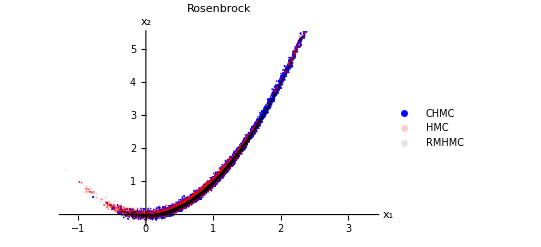

```mathematica
ListPlot[{QSchmc,QShmc,QSrhmc},PlotStyle->{Directive[Opacity[1],Blue],Directive[Opacity[.2],Red],Directive[Opacity[.1],Black]},PlotLegends->{Style["CHMC",Blue],Style["HMC",Red],Style["RMHMC",Black]},PlotLabel->Rosenbrock,AxesLabel->{"x_1","x_2"}]
```

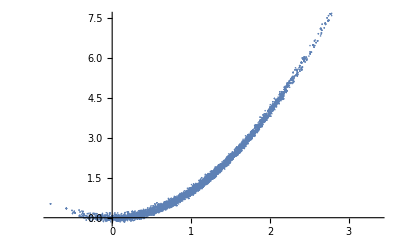

```mathematica
ListPlot[QSchmc]
```

10 chains trace

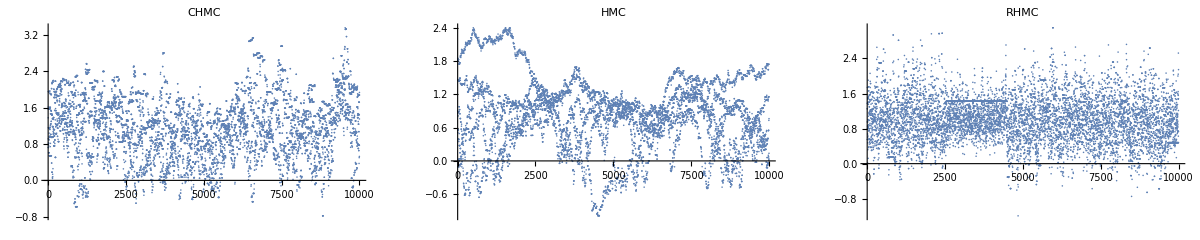

```mathematica
GraphicsRow[{ListPlot[QSchmc[[;;,1]],PlotLabel->"CHMC"],ListPlot[QShmc[[;;,1]],PlotLabel->"HMC"],ListPlot[QSrhmc[[;;,1]],PlotLabel->"RHMC"]}]
```